## Jacobi Functions

```mathematica
Manipulate[Plot[JacobiDN[p x,q],{x,0,2π}],{p,{1,2,3,4}},{q,{1/8,1/4,1/2}}]
```

For p = 2 EllipticK[q]/π

```mathematica
Manipulate[Plot[JacobiDN[(2 EllipticK[q]/π) x,q],{x,0,2π},PlotLabel->{q}],{q,{1/8,1/4,1/2}}]//Flatten
```

The function is periodic. Indeed

```mathematica
FullSimplify[JacobiDN[(2 EllipticK[q]/π)(x+2π),q]-JacobiDN[(2 EllipticK[q]/π)x,q]]
```

0

```mathematica
sol=Solve[JacobiDN[p x,q]^2+a JacobiSN[p x,q]^2==1,a]//First//FullSimplify
```

{a→q}

```mathematica
JacobiAmplitude[n EllipticK[q],q]/.{n->2,q->Random[]}
JacobiAmplitude[n EllipticK[q],q]/.{n->4,q->Random[]}
```

3.14159

6.28319

which is clearly π and 2π!

## Ansatz

```mathematica
u1=ⅇ^(ⅈ ω1 τ/κ)√q JacobiSN[(2 EllipticK[q]/π) σ,q];
u2=0;
u3=ⅇ^(ⅈ ω3 τ/κ)JacobiDN[(2 EllipticK[q]/π) σ,q];
{u1b,u3b}={u1,u3}/.Complex[a_,b_]->a-b I;
```

We are dealing with closed strings so we want the solutions to be periodic, hence we pick the p of the previous section. We should pick a of the previous section, to satisfy the condition in the sphere ū.u=1.

```mathematica
u={u1,u3};
ub={u1b,u3b};
```

```mathematica
solω=Solve[2 ⅈ κ D[u, τ]-D[u, {σ,2}]-2 u D[u, σ].D[ub, σ]==0,{ω1,ω3}]//FullSimplify//First//Quiet
```

{ω1→-(2 (-1+q) EllipticK[q]^2)/π^2,ω3→-(2 q EllipticK[q]^2)/π^2}

Check of Virasoro

```mathematica
{D[u, σ].D[ub, σ]-2 ⅈ κ ub.D[u, τ],ub.D[u, σ]}/.solω//FullSimplify
```

{0,0}

## Relation between q, κ and α,J

```mathematica
eqsJ=α J==∫_0^(2 π) (κ u1b u1-ⅈ u1b D[u1, τ])/(2 π)ⅆσ∧(1-α)J==∫_0^(2 π) (κ u3b u3-ⅈ u3b D[u3, τ])/(2 π)ⅆσ/.JacobiAmplitude[n_ EllipticK[q_],q_]:>n π/2/.solω
```

J α==-((2 EllipticE[q]-2 EllipticK[q]) (κ^2-(2 (-1+q) EllipticK[q]^2)/π^2))/(2 κ EllipticK[q])&&J (1-α)==(EllipticE[q] (κ^2-(2 q EllipticK[q]^2)/π^2))/(κ EllipticK[q])

```mathematica
{αJ,κJ}={α,κ}/.Solve[eqsJ,{α,κ}]//Series[#,{J,∞,1}]&//FullSimplify//Last//Normal
```

{1-EllipticE[q]/EllipticK[q],J+(2 EllipticK[q] (EllipticE[q]+(-1+q) EllipticK[q]))/(J π^2)}

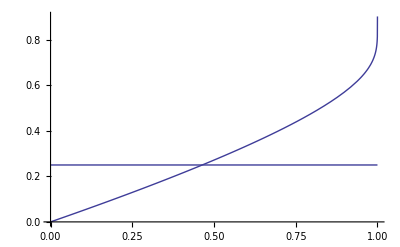

```mathematica
Show[Plot[αJ,{q,0,1}],Plot[0.25,{q,0,1}]]
```

```mathematica
solq=FindRoot[0.25-αJ,{q,0.4}]
```

{q→0.46401}

```mathematica
Energy=κJ/.solq
```

0.144398/J+J

```mathematica
v1=√α;v3=√(1-α);
```

```mathematica
analytical=1/(v1^2 v3^2)(∫_0^(2 π) (u1^2 u3b^2/.τ->0)/(2 π)ⅆσ)/.JacobiAmplitude[n_ EllipticK[q_],q_]:>n π/2/.Solve[1-EllipticE[q]/EllipticK[q]==α,EllipticE[q]]⟦1⟧//FullSimplify
```

(q+α-2 q α)/(3 α-3 α^2)

which is actually equivalent to (31) but way nicer.

```mathematica
rnumerical=1/(v1^2 v3^2)NIntegrate[1/(2π)(u1/.τ->0/.solq)^2(u3b/.τ->0/.solq)^2,{σ,0,2π}]/.α->1/4
```

0.856898

check:

```mathematica
analytical/.α->1/4/.solq
```

0.856898